1.04884

1.43091

1.67624

1.84137

1.96098

2.05607

2.1391

2.21723

2.29437

2.37245

2.45224

2.53385

2.61707

2.70153

2.78688

2.87279

2.95904

3.04551

3.13217

3.2191

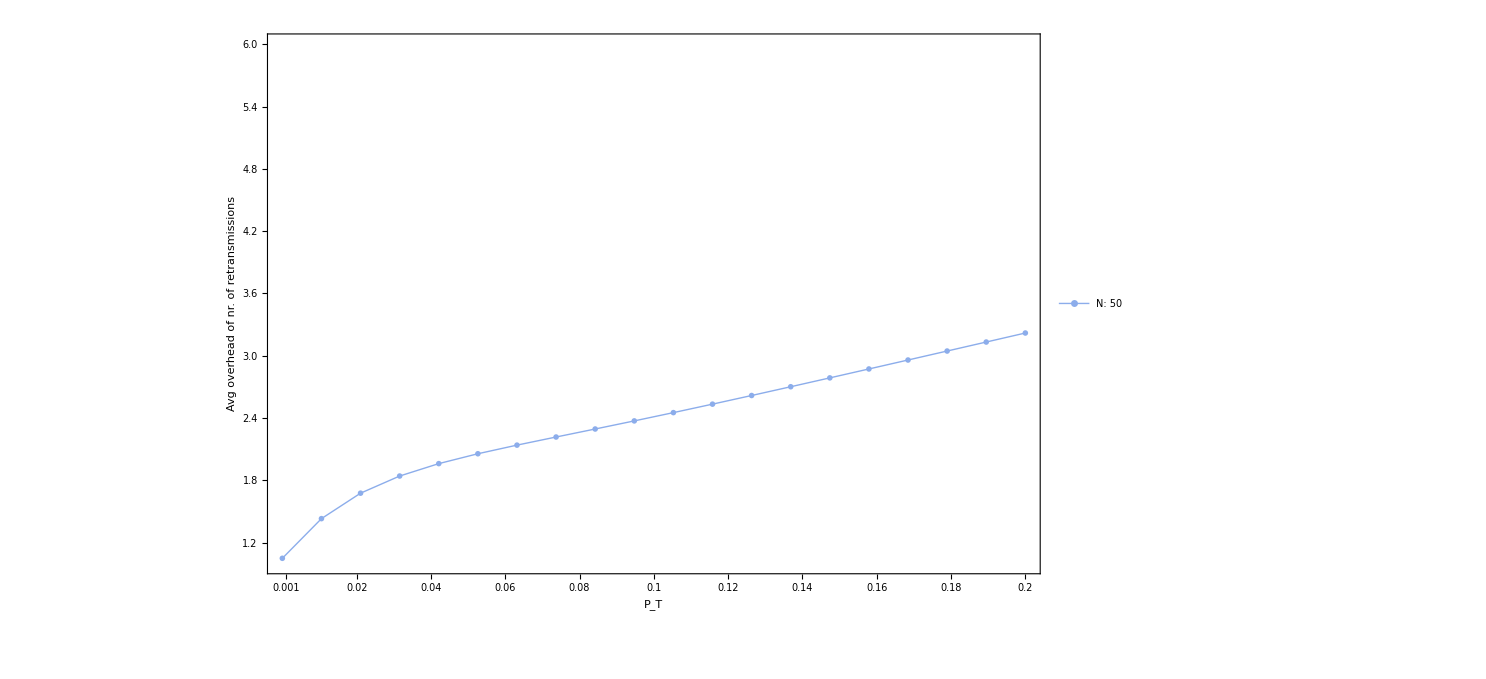

1.09531

1.68131

1.92435

2.05185

2.14681

2.23785

2.33326

2.43398

2.53848

2.64469

2.75077

2.8554

2.95784

3.05788

3.15575

3.25198

3.34726

3.44233

3.53788

3.63449

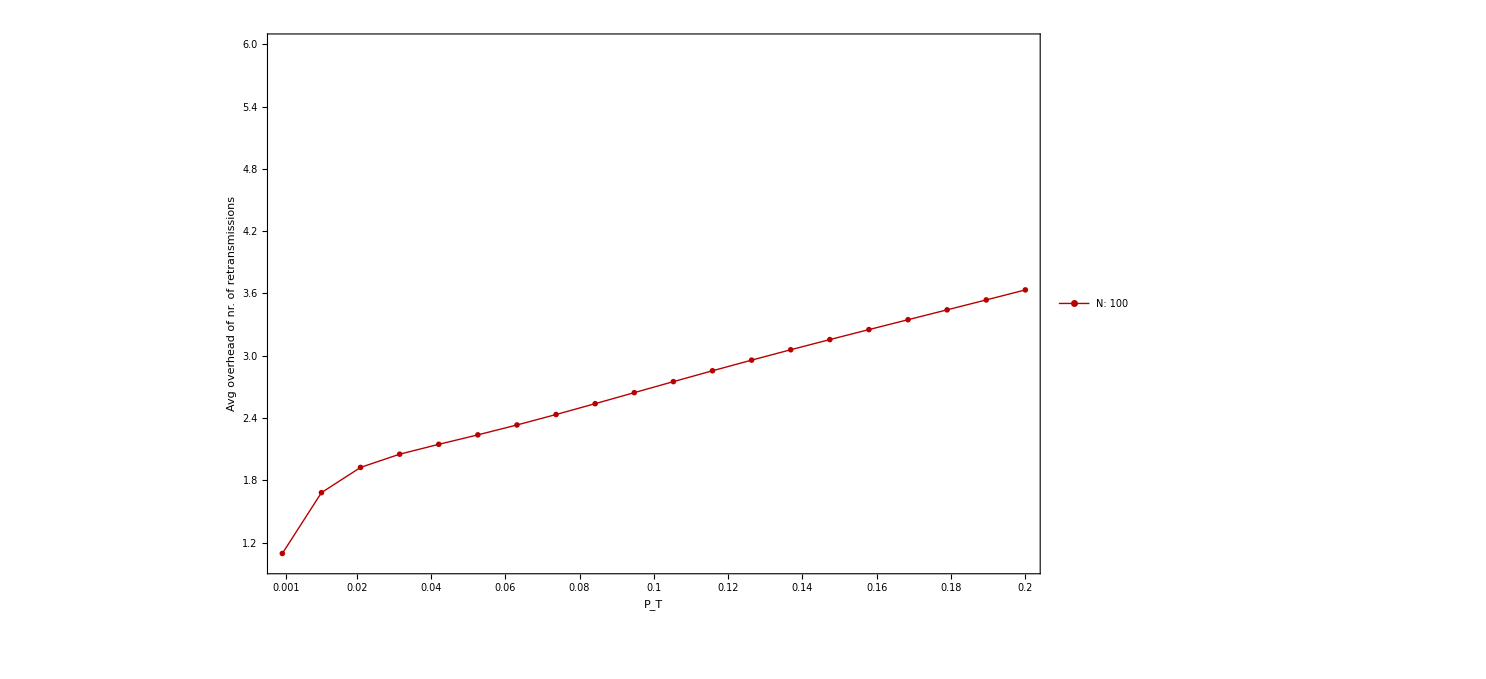

1.13951

1.82789

2.024

2.13002

2.23189

2.34377

2.46394

2.58779

2.7111

2.83091

2.9457

3.05521

3.16016

3.26184

3.36175

3.46129

3.56162

3.66351

3.76737

3.87333

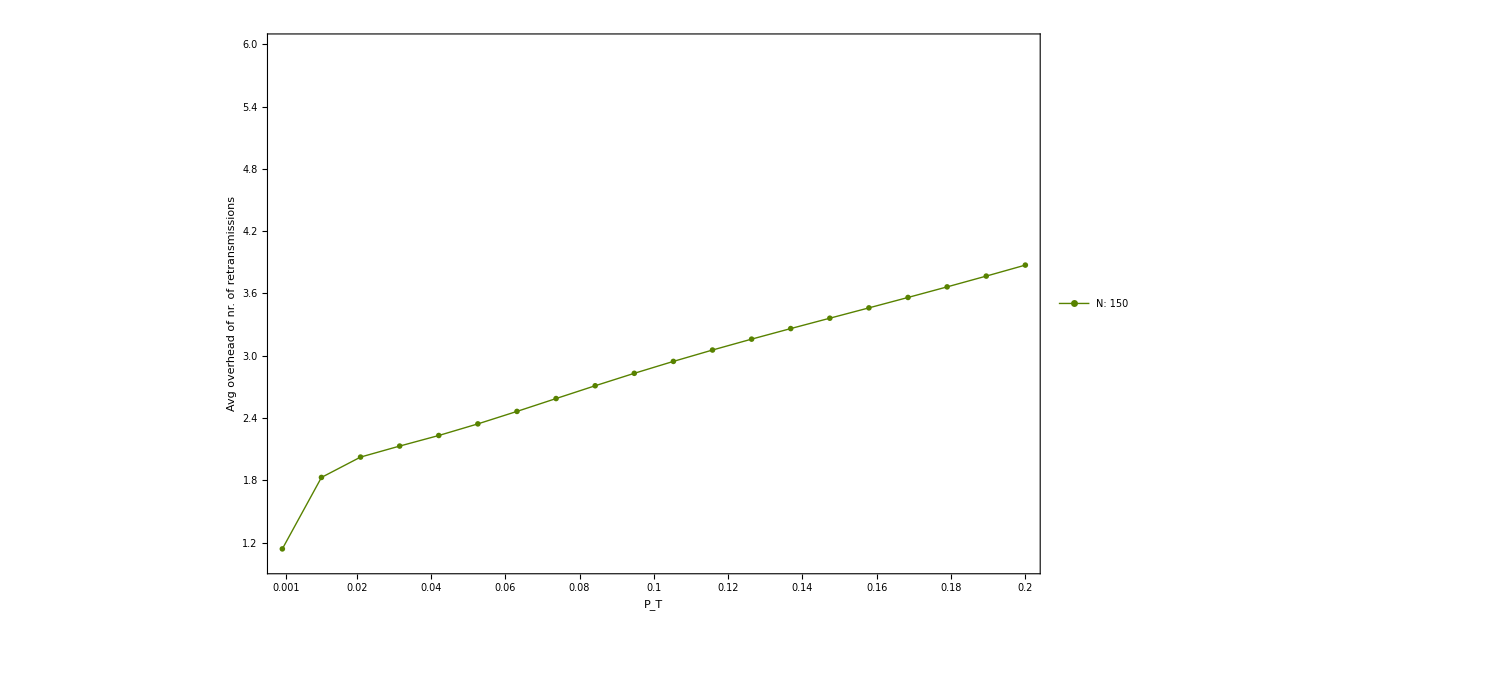

1.18155

1.91472

2.07199

2.17923

2.29977

2.43358

2.57287

2.7106

2.84213

2.9654

3.08059

3.18936

3.29408

3.39714

3.50052

3.60554

3.71283

3.8225

3.93429

4.04779

28.3465

```mathematica
(*
 DO:
 - no collision-related losses;
  - losses of retransmission requests due to wireless medium;
  - losses of informational packets due to wireless medium
GET:
- PMF on the number of retr. attempts to deliver a packet and message to all the stations;
  - PMF and CDF of the delay;
  - mean delay till all get the packet;
*)

(* Maxumun number of retransmissions, assumed to be infinity but this is enough *)
stepsMax=30;

(* Range of packet loss values *)
Pinit=0.001;
Pend  =0.7;
Pstep=0.01;

(* Number of stations *)
Ninit=50;
Nend=200;
Nstep=50;

(* Loss probability of retransmission packet *)

Unprotect[Power];
Power[0,0]=1;
Protect[Power];

pR=0;

(*Time to transmit the data packet (Tt) and retrnamission request (Tq), respectively, Tq<<Tt as data packets is usually longer *)
Tt= 0.01;
Tq= 0.001;

(* Time to wait to get the packet of interest as a result of the sent request *)

Tconst = 0.01;

(* Arrays to store PDF, CDF, Variance, Mean and quantile of the number of steps till absorbtion *)
singlePMFArray=Table[0*i*j*g*n,{i,1,(Pend-Pinit+Pstep)/Pstep,1},{j,1,(Nend-Ninit+Nstep)/Nstep,1},{g,1,2,1},{n,1,stepsMax}];
singleCDFArray=Table[0*i*j*g*n,{i,1,(Pend-Pinit+Pstep)/Pstep,1},{j,1,(Nend-Ninit+Nstep)/Nstep,1},{g,1,2,1},{n,1,stepsMax}];

singleVarArray=Table[0*i*j,{i,1,(Pend-Pinit+Pstep)/Pstep,1},{j,1,(Nend-Ninit+Nstep)/Nstep,1}];
singleMeanArray=Table[0*i*j,{i,1,(Pend-Pinit+Pstep)/Pstep,1},{j,1,(Nend-Ninit+Nstep)/Nstep,1}];


(* Arrays to store PDF, Mean and quantile of delay till absorbtion *)
singlePMFDelay=Table[0*i*j*g*n,{i,1,(Pend-Pinit+Pstep)/Pstep,1},{j,1,(Nend-Ninit+Nstep)/Nstep,1},{g,1,2,1},{n,1,stepsMax}];
singleMeanDelay=Table[0*i*j,{i,1,(Pend-Pinit+Pstep)/Pstep,1},{j,1,(Nend-Ninit+Nstep)/Nstep,1}];


(* Definiting Binomial distribution *)
BD[n_,p_,i_]:=Binomial[n,i]*(p^i)*(1-p)^n/(1-p)^i;

i=1;
j=1;

Do[
Do[

(* PARAMETERIZATION *)

(* Matrix Q of the absorbing Markov chain chain: jumping between transient states *)
Q=Table[0*k*n,{n,1,currN},{k,1,currN}];


For[n=1,n<currN+1,n++,
For[k=1,k<currN+1,k++,
If[k==n,If[n==currN,Part[Q,n,k]=Power[currP,n],Part[Q,n,k]=Power[pR,currN-n]+(1-Power[pR,currN-n])*Power[currP,n]]];
If[k<n,If[n==currN,Part[Q,n,k]=BD[n,currP,k],Part[Q,n,k]=(1-Power[pR,currN-n])*BD[n,currP,k]]];
];
];

(* Print["Matrix Q: ",TableForm[Q]]; *)

(* Defining vector t of the chain: absorbtion from every state *)
t=Table[0*n,{n,1,currN}];

For[n=1,n<currN+1,n++,
If[n≠currN,Part[t,n]=(1-Power[pR,currN-n])*(Power[1-currP,n]),Part[t,n]=Power[1-currP,currN]];
];

(* Print["vector t: ",TableForm[t]]; *)

(* Defining initial state probability vector: we always start with N stations not having a packet *)
v=Table[0*n,{n,1,currN}];
Part[v,currN]=1;

(* Print["vector v: ",TableForm[v]]; *)

(* COMPUTING METRICS FOR A SINGLE PACKET *)

(* Supplementary entities *)
e=Table[0*n+1,{n,1,currN}];

(* Print["vector e: ",TableForm[e]]; *)

(* PMF of the number of steps till absrobtion: gives PMF of the delay *)
stepsPMF=Table[v.If[n≠0,MatrixPower[Q,n],IdentityMatrix[currN]].t,{n,0,stepsMax}];

(* Print["stepsPMF: ",TableForm[stepsPMF]]; *)

(* Testing whether PMF sums up to one, if not increase the stepsMax*)
If[Sum[Part[stepsPMF,n],{n,0,stepsMax}]<0.99||Sum[Part[stepsPMF,n],{n,0,stepsMax}]>1.01,Print["PMF does not sum up to 1!"]];

(* Print["PMF sum to 1? ",TableForm[Sum[Part[stepsPMF,n],{n,1,stepsMax}]]]; *)

(* CDF of the number of steps till absrobtion: gives CDF of the delay *)

stepsCDF=Table[Sum[Part[stepsPMF,n],{n,1,k}],{k,1,stepsMax}];
(* Mean number of steps before absorbtion: gives mean delay *)
stepsMean=Sum[Part[stepsPMF,n]*n,{n,1,stepsMax}];

(* Print["steps Mean: ",TableForm[stepsMean]]; *)

(* Variance of the number of steps *)
stepsVar=Sum[Part[stepsPMF,n]*Power[(n-stepsMean),2],{n,1,stepsMax}];

(* Print["steps Variance: ",TableForm[stepsVar]]; *)

(* We can also get probabilities that k, k=1,2,..,N stations not having a packet after k step this is a vector: v*Q^{k} *)

(* Computing the Fundamental matrix *)
Z=Inverse[IdentityMatrix[currN]-Q];

(* Computing hi as the probability of being in the arbitrary state i after original transmission of the packet *)
(*h =Table [ PDF[BinomialDistribution[currN,pR],n],{n,0,currN}];*)

(* Probability of visiting a transient state j when starting in transient state i *)
Zdq=DiagonalMatrix[Diagonal[Z]];
visitPrMatrix=(Z-IdentityMatrix[currN]).Inverse[Zdq];

 (* Print["Matrix Z: ",TableForm[Z]]; *)

(* Print["Visits V: ",TableForm[visitPrMatrix]]; *)

(* CONDITIONAL DELAY IN A CERTAIN STATE *)
(* Array for conditional delays for failure and overall *)
condDelayFail=Table[0,{k,1,currN}];
condDelayAll=Table[0,{k,1,currN}];

(* Computing conditional delays for states starting from 1 to N-1: in case of failure *)
For [n=1,n<currN+1,n++,
  Part[condDelayFail,n] = Tconst;
];


(*
For [i=1,i<currN+1,i++,
 Print["Conditional delay fail ",i,":",TableForm[Part[condDelayFail,i]]];
];
*)


(* Computing the mean delay in the arbitrary state i *)
For [n=1,n<currN+1,n++,
Part[condDelayAll,n]= 1/Part[Q,n,n]*Part[condDelayFail,n]+ (Tq * (1-Power[pR,currN-n]) )+( Tt * (1-Power[currP,n]));
];

(*
For [i=1,i<currN+1,i++,
 Print["Conditional delay all ",i,": ",TableForm[Part[condDelayAll,i]]];
];
*)

(* Computing the mean delay till absorption *)

overallDelay =Tt + Sum[Part[condDelayAll,k]*Part[visitPrMatrix,n,k],{n,1,currN},{k,1,n}];

(* Print["Overall Delay: ",TableForm[overallDelay]]; *)

(* Storing PMF of the number of steps to global matrices*)
For[n=1,n<stepsMax+1,n++,
Part[singlePMFArray,i,j,2,n]=Part[stepsPMF,n];
Part[singlePMFArray,i,j,1,n]=n;
];


(* Print["PMF of steps till absorption: ",TableForm[singlePMFArray]]; *)

(* Storing CDF of the number of steps to global matrices*)
For[n=1,n<stepsMax+1,n++,
Part[singleCDFArray,i,j,2,n]=Part[stepsCDF,n];
Part[singleCDFArray,i,j,1,n]=n;
];

(* Print["CDF of steps till absorption: ",TableForm[singleCDFArray]]; *)

(* Storing Variance of the number of steps to global matrices*)
Part[singleVarArray,i,j]=stepsVar;
(* Print["Variance of steps till absorption: ",TableForm[singleVarArray]]; *)


(* Storing Mean of the number of steps to global matrices*)
Part[singleMeanArray,i,j]=stepsMean;
(* Print["Mean of the number of steps till absorption: ",TableForm[singleMeanArray]]; *)


(* Storing Mean of the delay to global matrices*)
Part[singleMeanDelay,i,j]=overallDelay;
(* Print["Mean of the delay till absorption: ",TableForm[singleMeanDelay]]; *)

(* PMF and CDF of delay not for this version *)



(* ENDING THE CYCLES *)
i++;,
{currP,Pinit,Pend,Pstep}];

i=1;
j++;,


{currN,Ninit,Nend,Nstep}];


(* taking average over PMFs for certain loss probabilities and number of stations to estimate the overhead of the extra traffic due to retransmissions *)

(*

y1=Sum[Part[singlePMFArray,1,1,2,z]*z,{z,1,30}]/30


y2=Sum[Part[singlePMFArray,2,1,2,z]*z,{z,1,30}]/30


y3=Sum[Part[singlePMFArray,3,1,2,z]*z,{z,1,30}]/30


y4=Sum[Part[singlePMFArray,4,1,2,z]*z,{z,1,30}]/30

y5=Sum[Part[singlePMFArray,5,1,2,z]*z,{z,1,30}]/30

y6=Sum[Part[singlePMFArray,6,1,2,z]*z,{z,1,30}]/30

y7=Sum[Part[singlePMFArray,7,1,2,z]*z,{z,1,30}]/30

y8=Sum[Part[singlePMFArray,8,1,2,z]*z,{z,1,30}]/30

y9=Sum[Part[singlePMFArray,9,1,2,z]*z,{z,1,30}]/30

y10=Sum[Part[singlePMFArray,10,1,2,z]*z,{z,1,30}]/30

y11=Sum[Part[singlePMFArray,11,1,2,z]*z,{z,1,30}]/30

(*
y12=Sum[Part[singlePMFArray,12,1,2,z]*z,{z,1,30}]
*)

markers1 = {{-Graphics-, 0.02}};
myplot1=ListPlot[Evaluate[{y1,y2,y3,y4,y5,y6,y7,y8,y9,y10,y11},Filling->None,Frame->True ,DataRange->{0.0,0.5},FrameTicks->{{Automatic,None},{{0,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5},None}},FrameLabel->{Style[Subscript[P,T],Black,25],Style["Avg overhead of retransmissions",Black,25]},PlotMarkers->markers1,PlotStyle->(Directive[AbsoluteThickness[1],#]&/@ColorData[95,"ColorList"]),ImageSize->800,Filling->{1->{2},2->{3},3->{4}},AxesOrigin->{0,0},Joined->True,PlotRange->All,PlotLegends->Placed[PointLegend[Row[{"N: 50"#}]&/@Range[4],LegendMarkers->markers1 ,LegendMarkerSize->12,LabelStyle->{GrayLevel[0.1],14}],{0.089,0.86}]],BaseStyle->{FontSize->20}]


(***)

y13=Sum[Part[singlePMFArray,1,2,2,z]*z,{z,1,30}]/30

y14=Sum[Part[singlePMFArray,2,2,2,z]*z,{z,1,30}]/30

y15=Sum[Part[singlePMFArray,3,2,2,z]*z,{z,1,30}]/30

y16=Sum[Part[singlePMFArray,4,2,2,z]*z,{z,1,30}]/30

y17=Sum[Part[singlePMFArray,5,2,2,z]*z,{z,1,30}]/30

y18=Sum[Part[singlePMFArray,6,2,2,z]*z,{z,1,30}]/30

y19=Sum[Part[singlePMFArray,7,2,2,z]*z,{z,1,30}]/30

y20=Sum[Part[singlePMFArray,8,2,2,z]*z,{z,1,30}]/30

y21=Sum[Part[singlePMFArray,9,2,2,z]*z,{z,1,30}]/30

y22=Sum[Part[singlePMFArray,10,2,2,z]*z,{z,1,30}]/30

y23=Sum[Part[singlePMFArray,11,2,2,z]*z,{z,1,30}]/30

(*
y24=Sum[Part[singlePMFArray,12,2,2,z]*z,{z,1,30}]
*)

markers2 = { {-Graphics-, 0.02}};
myplot2=ListPlot[Evaluate[{y13,y14,y15,y16,y17,y18,y19,y20,y21,y22,y23},Filling->None,Frame->True ,DataRange->{0.0,0.5},FrameTicks->{{Automatic,None},{{0,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5},None}},FrameLabel->{Style[Subscript[P,T],Black,25],Style["Avg overhead of retransmissions",Black,25]},PlotMarkers->markers2,PlotStyle->(Directive[AbsoluteThickness[1],#]&/@ColorData[85,"ColorList"]),ImageSize->800,Filling->{1->{2},2->{3},3->{4}},AxesOrigin->{0,0},Joined->True,PlotRange->All,PlotLegends->Placed[PointLegend[Row[{"N: 100"#}]&/@Range[4],LegendMarkers->markers2 ,LegendMarkerSize->12,LabelStyle->{GrayLevel[0.1],14}],{0.092,0.79}]],BaseStyle->{FontSize->20}]

(***)


y25=Sum[Part[singlePMFArray,1,3,2,z]*z,{z,1,30}]/30

y26=Sum[Part[singlePMFArray,2,3,2,z]*z,{z,1,30}]/30

y27=Sum[Part[singlePMFArray,3,3,2,z]*z,{z,1,30}]/30

y28=Sum[Part[singlePMFArray,4,3,2,z]*z,{z,1,30}]/30

y29=Sum[Part[singlePMFArray,5,3,2,z]*z,{z,1,30}]/30

y30=Sum[Part[singlePMFArray,6,3,2,z]*z,{z,1,30}]/30

y31=Sum[Part[singlePMFArray,7,3,2,z]*z,{z,1,30}]/30

y32=Sum[Part[singlePMFArray,8,3,2,z]*z,{z,1,30}]/30

y33=Sum[Part[singlePMFArray,9,3,2,z]*z,{z,1,30}]/30

y34=Sum[Part[singlePMFArray,10,3,2,z]*z,{z,1,30}]/30

y35=Sum[Part[singlePMFArray,11,3,2,z]*z,{z,1,30}]/30
(*
y36=Sum[Part[singlePMFArray,12,3,2,z]*z,{z,1,30}]
*)

markers3 = { {-Graphics-, 0.02}};
myplot3=ListPlot[Evaluate[{y25,y26,y27,y28,y29,y30,y31,y32,y33,y34,y35},Filling->None,Frame->True ,DataRange->{0.0,0.5},FrameTicks->{{Automatic,None},{{0,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5},None}},FrameLabel->{Style[Subscript[P,T],Black,25],Style["Avg overhead of retransmissions",Black,25]},PlotMarkers->markers3,PlotStyle->(Directive[AbsoluteThickness[1],#]&/@ColorData[75,"ColorList"]),ImageSize->800,Filling->{1->{2},2->{3},3->{4}},AxesOrigin->{0,0},Joined->True,PlotRange->All,PlotLegends->Placed[PointLegend[Row[{"N: 150"#}]&/@Range[4],LegendMarkers->markers3 ,LegendMarkerSize->12,LabelStyle->{GrayLevel[0.1],14}],{0.092,0.72}]],BaseStyle->{FontSize->20}]
(***)

y37=Sum[Part[singlePMFArray,1,4,2,z]*z,{z,1,30}]/30

y38=Sum[Part[singlePMFArray,2,4,2,z]*z,{z,1,30}]/30

y39=Sum[Part[singlePMFArray,3,4,2,z]*z,{z,1,30}]/30

y40=Sum[Part[singlePMFArray,4,4,2,z]*z,{z,1,30}]/30

y41=Sum[Part[singlePMFArray,5,4,2,z]*z,{z,1,30}]/30

y42=Sum[Part[singlePMFArray,6,4,2,z]*z,{z,1,30}]/30

y43=Sum[Part[singlePMFArray,7,4,2,z]*z,{z,1,30}]/30

y44=Sum[Part[singlePMFArray,8,4,2,z]*z,{z,1,30}]/30

y45=Sum[Part[singlePMFArray,9,4,2,z]*z,{z,1,30}]/30

y46=Sum[Part[singlePMFArray,10,4,2,z]*z,{z,1,30}]/30

y47=Sum[Part[singlePMFArray,11,4,2,z]*z,{z,1,30}]/30
(*
y48=Sum[Part[singlePMFArray,12,4,2,z]*z,{z,1,30}]
*)

markers4 = {{-Graphics-, 0.02}};

myplot4=ListPlot[Evaluate[{y37,y38,y39,y40,y41,y42,y43,y44,y45,y46,y47},Filling->None,Frame->True ,DataRange->{0.0,0.5},FrameTicks->{{Automatic,None},{{0,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5},None}},FrameLabel->{Style[Subscript[P,T],Black,25],Style["Avg overhead of retransmissions",Black,25]},PlotMarkers->markers4,PlotStyle->(Directive[AbsoluteThickness[1],#]&/@ColorData[65,"ColorList"]),ImageSize->800,Filling->{1->{2},2->{3},3->{4}},AxesOrigin->{0,0},Joined->True,PlotRange->All,PlotLegends->Placed[PointLegend[Row[{"N: 200"#}]&/@Range[4],LegendMarkers->markers4 ,LegendMarkerSize->12,LabelStyle->{GrayLevel[0.1],14}],{0.092,0.65}]],BaseStyle->{FontSize->20}]



cm=72/2.54 (*centimetres*)
Show[myplot1,myplot2,myplot3,myplot4]
Export["AVG-overhead-normalized.eps",Show[myplot1,myplot2,myplot3,myplot4,ImageSize->19 cm]]
*)

y1=Sum[Part[singlePMFArray,1,1,2,z]*z,{z,1,30}]


y2=Sum[Part[singlePMFArray,2,1,2,z]*z,{z,1,30}]


y3=Sum[Part[singlePMFArray,3,1,2,z]*z,{z,1,30}]


y4=Sum[Part[singlePMFArray,4,1,2,z]*z,{z,1,30}]

y5=Sum[Part[singlePMFArray,5,1,2,z]*z,{z,1,30}]

y6=Sum[Part[singlePMFArray,6,1,2,z]*z,{z,1,30}]

y7=Sum[Part[singlePMFArray,7,1,2,z]*z,{z,1,30}]

y8=Sum[Part[singlePMFArray,8,1,2,z]*z,{z,1,30}]

y9=Sum[Part[singlePMFArray,9,1,2,z]*z,{z,1,30}]

y10=Sum[Part[singlePMFArray,10,1,2,z]*z,{z,1,30}]

y11=Sum[Part[singlePMFArray,11,1,2,z]*z,{z,1,30}]

y12=Sum[Part[singlePMFArray,12,1,2,z]*z,{z,1,30}]

y13=Sum[Part[singlePMFArray,13,1,2,z]*z,{z,1,30}]

y14=Sum[Part[singlePMFArray,14,1,2,z]*z,{z,1,30}]

y15=Sum[Part[singlePMFArray,15,1,2,z]*z,{z,1,30}]

y16=Sum[Part[singlePMFArray,16,1,2,z]*z,{z,1,30}]

y17=Sum[Part[singlePMFArray,17,1,2,z]*z,{z,1,30}]

y18=Sum[Part[singlePMFArray,18,1,2,z]*z,{z,1,30}]

y19=Sum[Part[singlePMFArray,19,1,2,z]*z,{z,1,30}]

y20=Sum[Part[singlePMFArray,20,1,2,z]*z,{z,1,30}]


markers1 = {{-Graphics-, 0.02}};
myplot1=ListPlot[Evaluate[{y1,y2,y3,y4,y5,y6,y7,y8,y9,y10,y11,y12,y13,y14,y15,y16,y17,y18,y19,y20},Filling->None,Frame->True ,DataRange->{0.0,0.2},FrameTicks->{{Automatic,None},{{0.001,0.02,0.04,0.06,0.08,0.1,0.12,0.14,0.16,0.18,0.2},None}},FrameTicksStyle->{{Black,Black},{Black,Black}},FrameLabel->{Style[Subscript[P,T],Black,40],Style["Avg overhead of nr. of retransmissions",Black,40]},PlotMarkers->markers1,PlotStyle->(Directive[AbsoluteThickness[1],#]&/@ColorData[95,"ColorList"]),ImageSize->1100,Filling->{1->{2},2->{3},3->{4}},AxesOrigin->{0,0},Joined->True,PlotRange->{1,6},PlotLegends->Placed[PointLegend[Row[{"N: 50"#}]&/@Range[4],LegendMarkers->markers1 ,LegendMarkerSize->30,LabelStyle->{Black,28}],{0.095,0.9}]],BaseStyle->{FontSize->40,FontColor->Black, FontFamily->"Times New Roman"},FrameStyle->Directive[Black]]


(***)

y21=Sum[Part[singlePMFArray,1,2,2,z]*z,{z,1,30}]

y22=Sum[Part[singlePMFArray,2,2,2,z]*z,{z,1,30}]

y23=Sum[Part[singlePMFArray,3,2,2,z]*z,{z,1,30}]

y24=Sum[Part[singlePMFArray,4,2,2,z]*z,{z,1,30}]

y25=Sum[Part[singlePMFArray,5,2,2,z]*z,{z,1,30}]

y26=Sum[Part[singlePMFArray,6,2,2,z]*z,{z,1,30}]

y27=Sum[Part[singlePMFArray,7,2,2,z]*z,{z,1,30}]

y28=Sum[Part[singlePMFArray,8,2,2,z]*z,{z,1,30}]

y29=Sum[Part[singlePMFArray,9,2,2,z]*z,{z,1,30}]

y30=Sum[Part[singlePMFArray,10,2,2,z]*z,{z,1,30}]

y31=Sum[Part[singlePMFArray,11,2,2,z]*z,{z,1,30}]

y32=Sum[Part[singlePMFArray,12,2,2,z]*z,{z,1,30}]

y33=Sum[Part[singlePMFArray,13,2,2,z]*z,{z,1,30}]

y34=Sum[Part[singlePMFArray,14,2,2,z]*z,{z,1,30}]

y35=Sum[Part[singlePMFArray,15,2,2,z]*z,{z,1,30}]

y36=Sum[Part[singlePMFArray,16,2,2,z]*z,{z,1,30}]

y37=Sum[Part[singlePMFArray,17,2,2,z]*z,{z,1,30}]

y38=Sum[Part[singlePMFArray,18,2,2,z]*z,{z,1,30}]

y39=Sum[Part[singlePMFArray,19,2,2,z]*z,{z,1,30}]

y40=Sum[Part[singlePMFArray,20,2,2,z]*z,{z,1,30}]


markers2 = { {-Graphics-, 0.02}};
myplot2=ListPlot[Evaluate[{y21,y22,y23,y24,y25,y26,y27,y28,y29,y30,y31,y32,y33,y34,y35,y36,y37,y38,y39,y40},Filling->None,Frame->True ,DataRange->{0.0,0.2},FrameTicks->{{Automatic,None},{{0.001,0.02,0.04,0.06,0.08,0.1,0.12,0.14,0.16,0.18,0.2},None}},FrameTicksStyle->{{Black,Black},{Black,Black}},FrameLabel->{Style[Subscript[P,T],Black,40],Style["Avg overhead of nr. of retransmissions",Black,40]},PlotMarkers->markers2,PlotStyle->(Directive[AbsoluteThickness[1],#]&/@ColorData[85,"ColorList"]),ImageSize->1100,Filling->{1->{2},2->{3},3->{4}},AxesOrigin->{0,0},Joined->True,PlotRange->{1,6},PlotLegends->Placed[PointLegend[Row[{"N: 100"#}]&/@Range[4],LegendMarkers->markers2 ,LegendMarkerSize->30,LabelStyle->{Black,28}],{0.1,0.83}]],BaseStyle->{FontSize->40,FontColor->Black, FontFamily->"Times New Roman"},FrameStyle->Directive[Black]]

(***)

y41=Sum[Part[singlePMFArray,1,3,2,z]*z,{z,1,30}]

y42=Sum[Part[singlePMFArray,2,3,2,z]*z,{z,1,30}]

y43=Sum[Part[singlePMFArray,3,3,2,z]*z,{z,1,30}]

y44=Sum[Part[singlePMFArray,4,3,2,z]*z,{z,1,30}]

y45=Sum[Part[singlePMFArray,5,3,2,z]*z,{z,1,30}]

y46=Sum[Part[singlePMFArray,6,3,2,z]*z,{z,1,30}]

y47=Sum[Part[singlePMFArray,7,3,2,z]*z,{z,1,30}]

y48=Sum[Part[singlePMFArray,8,3,2,z]*z,{z,1,30}]

y49=Sum[Part[singlePMFArray,9,3,2,z]*z,{z,1,30}]

y50=Sum[Part[singlePMFArray,10,3,2,z]*z,{z,1,30}]

y51=Sum[Part[singlePMFArray,11,3,2,z]*z,{z,1,30}]

y52=Sum[Part[singlePMFArray,12,3,2,z]*z,{z,1,30}]

y53=Sum[Part[singlePMFArray,13,3,2,z]*z,{z,1,30}]

y54=Sum[Part[singlePMFArray,14,3,2,z]*z,{z,1,30}]

y55=Sum[Part[singlePMFArray,15,3,2,z]*z,{z,1,30}]

y56=Sum[Part[singlePMFArray,16,3,2,z]*z,{z,1,30}]

y57=Sum[Part[singlePMFArray,17,3,2,z]*z,{z,1,30}]

y58=Sum[Part[singlePMFArray,18,3,2,z]*z,{z,1,30}]

y59=Sum[Part[singlePMFArray,19,3,2,z]*z,{z,1,30}]

y60=Sum[Part[singlePMFArray,20,3,2,z]*z,{z,1,30}]


markers3 = { {-Graphics-, 0.02}};
myplot3=ListPlot[Evaluate[{y41,y42,y43,y44,y45,y46,y47,y48,y49,y50,y51,y52,y53,y54,y55,y56,y57,y58,y59,y60},Filling->None,Frame->True ,DataRange->{0.0,0.2},FrameTicks->{{Automatic,None},{{0.001,0.02,0.04,0.06,0.08,0.1,0.12,0.14,0.16,0.18,0.2},None}},FrameTicksStyle->{{Black,Black},{Black,Black}},FrameLabel->{Style[Subscript[P,T],Black,40],Style["Avg overhead of nr. of retransmissions",Black,40]},PlotMarkers->markers3,PlotStyle->(Directive[AbsoluteThickness[1],#]&/@ColorData[75,"ColorList"]),ImageSize->1100,Filling->{1->{2},2->{3},3->{4}},AxesOrigin->{0,0},Joined->True,PlotRange->{1,6},PlotLegends->Placed[PointLegend[Row[{"N: 150"#}]&/@Range[4],LegendMarkers->markers3 ,LegendMarkerSize->30,LabelStyle->{Black,28}],{0.1,0.76}]],BaseStyle->{FontSize->40,FontColor->Black, FontFamily->"Times New Roman"},FrameStyle->Directive[Black]]
(***)

y61=Sum[Part[singlePMFArray,1,4,2,z]*z,{z,1,30}]

y62=Sum[Part[singlePMFArray,2,4,2,z]*z,{z,1,30}]

y63=Sum[Part[singlePMFArray,3,4,2,z]*z,{z,1,30}]

y64=Sum[Part[singlePMFArray,4,4,2,z]*z,{z,1,30}]

y65=Sum[Part[singlePMFArray,5,4,2,z]*z,{z,1,30}]

y66=Sum[Part[singlePMFArray,6,4,2,z]*z,{z,1,30}]

y67=Sum[Part[singlePMFArray,7,4,2,z]*z,{z,1,30}]

y68=Sum[Part[singlePMFArray,8,4,2,z]*z,{z,1,30}]

y69=Sum[Part[singlePMFArray,9,4,2,z]*z,{z,1,30}]

y70=Sum[Part[singlePMFArray,10,4,2,z]*z,{z,1,30}]

y71=Sum[Part[singlePMFArray,11,4,2,z]*z,{z,1,30}]

y72=Sum[Part[singlePMFArray,12,4,2,z]*z,{z,1,30}]

y73=Sum[Part[singlePMFArray,13,4,2,z]*z,{z,1,30}]

y74=Sum[Part[singlePMFArray,14,4,2,z]*z,{z,1,30}]

y75=Sum[Part[singlePMFArray,15,4,2,z]*z,{z,1,30}]

y76=Sum[Part[singlePMFArray,16,4,2,z]*z,{z,1,30}]

y77=Sum[Part[singlePMFArray,17,4,2,z]*z,{z,1,30}]

y78=Sum[Part[singlePMFArray,18,4,2,z]*z,{z,1,30}]

y79=Sum[Part[singlePMFArray,19,4,2,z]*z,{z,1,30}]

y80=Sum[Part[singlePMFArray,20,4,2,z]*z,{z,1,30}]


markers4 = {{-Graphics-, 0.02}};

myplot4=ListPlot[Evaluate[{y61,y62,y63,y64,y65,y66,y67,y68,y69,y70,y71,y72,y73,y74,y75,y76,y77,y78,y79,y80},Filling->None,Frame->True ,DataRange->{0.0,0.2},FrameTicks->{{Automatic,None},{{0.001,0.02,0.04,0.06,0.08,0.1,0.12,0.14,0.16,0.18,0.2},None}},FrameTicksStyle->{{Black,Black},{Black,Black}},FrameLabel->{Style[Subscript[P,T],Black,40],Style["Avg overhead of nr. of retransmissions",Black,40]},PlotMarkers->markers4,PlotStyle->(Directive[AbsoluteThickness[1],#]&/@ColorData[65,"ColorList"]),ImageSize->1100,Filling->{1->{2},2->{3},3->{4}},AxesOrigin->{0,0},Joined->True,PlotRange->{1,6},PlotLegends->Placed[PointLegend[Row[{"N: 200"#}]&/@Range[4],LegendMarkers->markers4 ,LegendMarkerSize->30,LabelStyle->{Black,28}],{0.1,0.69}]],BaseStyle->{FontSize->40,FontColor->Black, FontFamily->"Times New Roman"},FrameStyle->Directive[Black]]


cm=72/2.54 (*centimetres*)
Show[myplot1,myplot2,myplot3,myplot4]
Export["AVG-overhead-retrans.eps",Show[myplot1,myplot2,myplot3,myplot4,ImageSize->20 cm]]
```

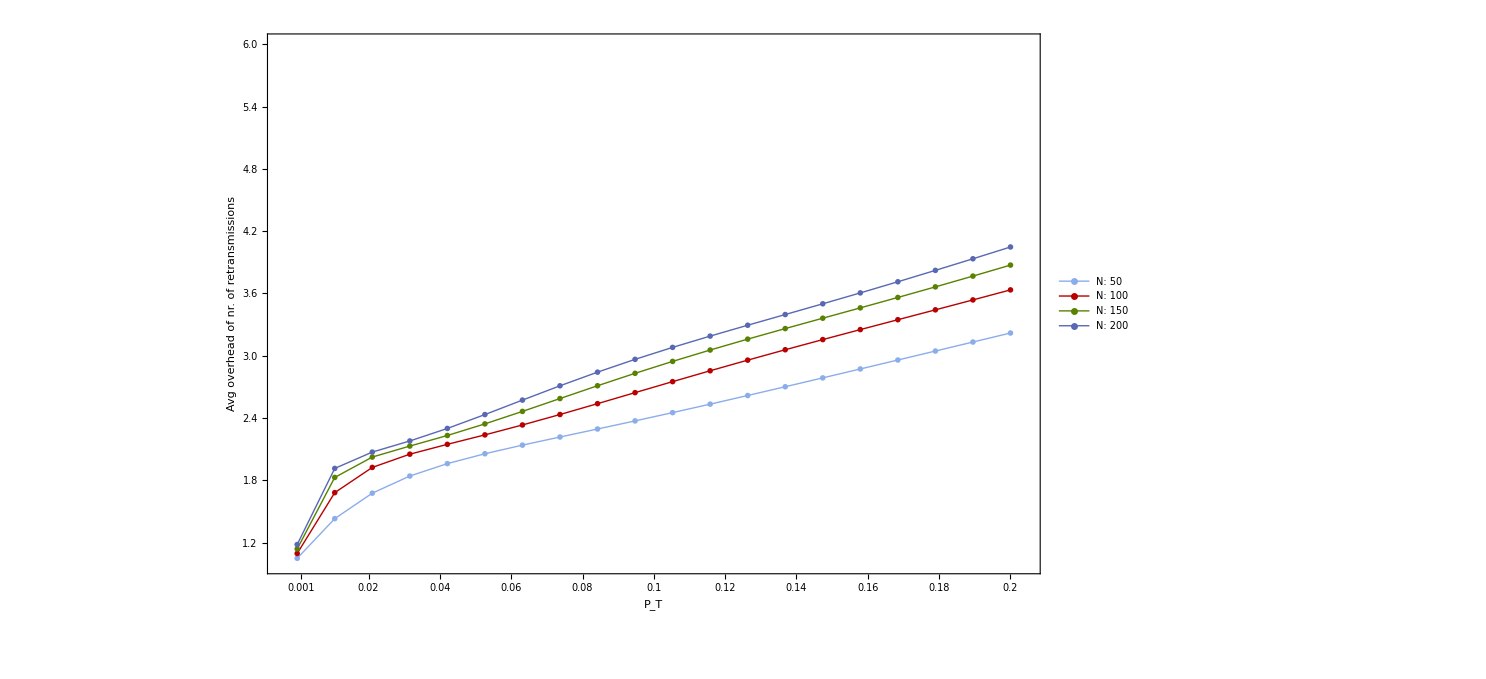

AVG-overhead-retrans.eps

AVG-overhead.eps